Universidad de Jaén. Escuela Politécnica Superior de Jaén.
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. Curso 2024/25
F.Javier Muñoz Delgado

# TEMA 12: ECUACIONES NO LINEALES. Notas y prácticas.

# Teorema de Bolzano. Método de bisección.

En cursos anteriores se estudió la resolución de ecuaciones lineales de la forma
						2x + 3 = 7.
También se estudiaron ecuaciones de segundo grado de la forma
					2 x^2 + 3 x - 2 = 0.
Para polinomios de mayor grado se presentó el método de Ruffini. El método de Ruffini permite hacer de forma rápida la división de un polinomio por otro de la forma (x-r). En el caso en que el resto sea cero, significa que r es una raíz. Pero, ¿cómo acertar con el valor de r que es una raíz? Hay teoremas que en el caso de polinomios con coeficientes enteros nos dicen cómo pueden ser las raíces reales del polinomio en el caso en que existan. En cursos anteriores, se consideraban polinomios con coeficiente líder igual a 1 y el resto coeficientes enteros, y se probaba con los divisores del término independiente. El problema es que hay muchos polinomios que no tienen todos los coeficientes enteros, o que no tienen todas sus raíces racionales (salvo que el problema esté “preparado”). En general, no sabemos cómo encontrar las raíces de un polinomio. Para ecuaciones polinómicas de grado cinco o superior no existen fórmulas que nos den las raíces, por tanto, en general, debemos recurrir a métodos numéricos. 

Además, podemos considerar ecuaciones que no sean polinómicas,
			x + ⅇ^x = cos x 
En general, salvo excepciones, no tenemos métodos para poder abordar este tipo de ecuaciones.

Buscando entre los resultados teóricos conocidos, encontramos el Teorema de Bolzano.
Teorema de Bolzano. Si f es una función continua en un intervalo [a,b] y f toma signos opuestos en los extremos (es decir, f(a)f(b)<0), existe un punto c en (a,b) tal que f(c)=0.

Por ello cuando nos encontremos con una ecuación podríamos pasar todo a un miembro, quedando igualado a cero. Usualmente, la expresión que aparece es una función continua. En ese caso, bastaría encontrar un intervalo donde la función esté definida y que en los extremos la función tenga signos opuestos para así asegurar que hay una solución de la ecuación f(x)=0 en el interior del intervalo. Además, dividiendo sucesivamente el intervalo inicial podremos llegar a encontrar un intervalo de longitud tan pequeña como queramos que incluya a la solución de la ecuación.

El método de bisección consiste en reducir el intervalo (manteniendo el cambio de signo de la función) dividiéndolo por la mitad en cada paso. Si el intervalo inicial mide b-a, después de n divisiones, el intervalo medirá (b-a)/2^n. Podríamos decir que conocemos que la solución está entre dos valores tan cercanos como queramos.

Con el Mathematica podemos hacer pequeños programas (o grandes) para implementar los métodos numéricos.

En este caso, introducimos la función y el intervalo donde queremos comenzar. Tras comprobar si hay cambio de signo de la función, con la función Do hacemos particiones del intervalo, reduciendo en cada caso por el lado donde no hay cambio de signo, y nos dice el intervalo que queda.

#### Método de Bisección

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=x^2-2
```

```mathematica
Plot[f[x],{x,-3,3}]
```

-Graphics-

En este caso, tenemos una función sencilla de la que conocemos su gráfica y la solución de la ecuación f(x)=0.

```mathematica
a=0;b=3;If[f[a]f[b]<0,Do[If[f[(a+b)/2]f[a]>0,a=(a+b)/2,b=(a+b)/2],{20}];Print["La solución está entre ",N[a,10]," y ",N[b,10],". Una aproximación sería ",N[(a+b)/2,10],". La función en este punto vale ",N[f[(a+b)/2],10]],
Print["No hay cambio de signo: cambiar los puntos."]];
```

La solución está entre 1.414212227 y 1.414215088. Una aproximación sería 1.414213657. La función en este punto vale 2.68717713×10^-7

Si quisiéramos ver todo lo obtenido:

```mathematica
a=0;b=3;
Print["En ",a," la función vale ",N[f[a]], " y en ",b, " vale ", N[f[b],10]];If[f[a]f[b]<0,Do[If[f[(a+b)/2]f[a]>0,a=(a+b)/2,b=(a+b)/2];Print["Está entre ",a," y ",b,". En ",(a+b)/2," la función vale ",N[f[(a+b)/2],10]],{20}],
Print["No hay cambio de signo. Cambia los puntos."]]; Print["La solución está entre ",N[a,10]," y ",N[b,10],". Una aproximación sería ",N[(a+b)/2,10],". La función vale ",N[f[(a+b)/2],10]]
```

En 0 la función vale -2. y en 3 vale 7.

Está entre 0 y 3/2. En 3/4 la función vale -1.4375

Está entre 3/4 y 3/2. En 9/8 la función vale -0.734375

Está entre 9/8 y 3/2. En 21/16 la función vale -0.27734375

Está entre 21/16 y 3/2. En 45/32 la función vale -0.0224609375

Está entre 45/32 y 3/2. En 93/64 la función vale 0.1115722656

Está entre 45/32 y 93/64. En 183/128 la función vale 0.04400634766

Está entre 45/32 y 183/128. En 363/256 la función vale 0.01063537598

Está entre 45/32 y 363/256. En 723/512 la función vale -0.005947113037

Está entre 723/512 y 363/256. En 1449/1024 la función vale 0.002335548401

Está entre 723/512 y 1449/1024. En 2895/2048 la función vale -0.001807928085

Está entre 2895/2048 y 1449/1024. En 5793/4096 la función vale 0.000263273716

Está entre 2895/2048 y 5793/4096. En 11583/8192 la función vale -0.0007724612951

Está entre 11583/8192 y 5793/4096. En 23169/16384 la función vale -0.0002546273172

Está entre 23169/16384 y 5793/4096. En 46341/32768 la función vale 4.314817488×10^-6

Está entre 23169/16384 y 46341/32768. En 92679/65536 la función vale -0.0001251583453

Está entre 92679/65536 y 46341/32768. En 185361/131072 la función vale -0.00006042228779

Está entre 185361/131072 y 46341/32768. En 370725/262144 la función vale -0.00002805386612

Está entre 370725/262144 y 46341/32768. En 741453/524288 la función vale -0.00001186955706

Está entre 741453/524288 y 46341/32768. En 1482909/1048576 la función vale -3.77737797×10^-6

Está entre 1482909/1048576 y 46341/32768. En 2965821/2097152 la función vale 2.68717713×10^-7

La solución está entre 1.414212227 y 1.414215088. Una aproximación sería 1.414213657. La función vale 2.68717713×10^-7

Hay varias posibilidades de parada, además del número de iteraciones (en este caso 20); Amplitud del intervalo (“cifras exactas”), valor de la función, ... Individualmente, o combinadas.

#### Método de Regula-Falsi

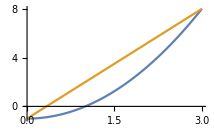
En el Método de Regula-Falsi, en lugar de tomar siempre el punto medio del intervalo, se toma un valor intermedio dependiendo de los valores de la función en los extremos (más cerca del extremo donde la función esté más próxima a cero).
								-Graphics-
Sería decir que el punto intermedio, en lugar del que toma el Método de Bisección, (a+b)/2, sea un x tal que (x-a)/(f(a))=(x-b)/(f(b)), despejando, x = (a f(b)-b f(a))/(f(b)-f(a)). Posteriormente, nos quedaremos con el trozo [a,x] o [x,b]  donde se produzca el cambio de signo de la función. Es equivalente a tomar una recta que pase por (a, f(a)) y (b,f(b)) y buscar dónde esta recta vale 0.

Calculamos el polinomio que interpola, y buscamos la expresión del cero de la recta que pasa por esos dos puntos.

```mathematica
Clear["Global`*"]
```

```mathematica
Solve[InterpolatingPolynomial[{{a,fa},{b,fb}},x]==0,x]//Simplify
```

{{x→(b fa-a fb)/(fa-fb)}}

```mathematica
f[x_]:=x^2-2
```

```mathematica
a=0;b=3;If[f[a]f[b]<0,Do[If[f[(a f[b]-b f[a])/(f[b]-f[a])]f[a]>0,a=(a f[b]-b f[a])/(f[b]-f[a]),b=(a f[b]-b f[a])/(f[b]-f[a])],{20}];Print["La solución está entre ",N[a,10]," y ",N[b,10],". Una aproximación sería ",N[(a f[b]-b f[a])/(f[b]-f[a]),10],". La función vale ",N[f[(a f[b]-b f[a])/(f[b]-f[a])],10]],
Print["No hay cambio de signo. Cambia los puntos."]];
```

La solución está entre 1.414213559 y 3.. Una aproximación sería 1.414213561. La función vale -3.683905784×10^-9

Si queremos ir viendo los valores que se van obteniendo:

```mathematica
a=0;b=3;If[f[a]f[b]<0,Do[If[f[(a f[b]-b f[a])/(f[b]-f[a])]f[a]>0,a=(a f[b]-b f[a])/(f[b]-f[a]),b=(a f[b]-b f[a])/(f[b]-f[a])];Print["Entre ",N[a,10]," y ",N[b,10],". En ",N[(a f[b]-b f[a])/(f[b]-f[a]),10]," la función vale ",N[f[(a f[b]-b f[a])/(f[b]-f[a])],10]],{20}],
Print["No hay cambio de signo. Cambia los puntos."]];
```

Entre 0.6666666667 y 3.. En 1.090909091 la función vale -0.8099173554

Entre 1.090909091 y 3.. En 1.288888889 la función vale -0.3387654321

Entre 1.288888889 y 3.. En 1.367875648 la función vale -0.1289162125

Entre 1.367875648 y 3.. En 1.397390273 la función vale -0.04730042539

Entre 1.397390273 y 3.. En 1.408146749 la función vale -0.01712273217

Entre 1.408146749 y 3.. En 1.412031087 la función vale -0.006168208078

Entre 1.412031087 y 3.. En 1.41342913 la función vale -0.002218093903

Entre 1.41342913 y 3.. En 1.413931709 la función vale -0.0007971235752

Entre 1.413931709 y 3.. En 1.414112301 la función vale -0.0002863996446

Entre 1.414112301 y 3.. En 1.414177184 la función vale -0.0001028925093

Entre 1.414177184 y 3.. En 1.414200493 la función vale -0.00003696428205

Entre 1.414200493 y 3.. En 1.414208867 la función vale -0.00001327933128

Entre 1.414208867 y 3.. En 1.414211876 la función vale -4.770550392×10^-6

Entre 1.414211876 y 3.. En 1.414212956 la función vale -1.713800156×10^-6

Entre 1.414212956 y 3.. En 1.414213345 la función vale -6.156751938×10^-7

Entre 1.414213345 y 3.. En 1.414213484 la función vale -2.211785757×10^-7

Entre 1.414213484 y 3.. En 1.414213534 la función vale -7.945741481×10^-8

Entre 1.414213534 y 3.. En 1.414213552 la función vale -2.85447205×10^-8

Entre 1.414213552 y 3.. En 1.414213559 la función vale -1.025456295×10^-8

Entre 1.414213559 y 3.. En 1.414213561 la función vale -3.683905784×10^-9

Observemos que uno de los extremos queda fijo (el intervalo no tiende a tener longitud cero), aunque hay cambio de signo en los extremos. Sin embargo, el valor encontrado en este ejemplo, tras 20 iteraciones es “mejor” que el encontrado en el método de bisección (la función toma un valor mucho más cercano al cero).

Decíamos antes que el método de regula falsi era como tomar como siguiente valor el punto donde la recta que interpola se anula. Veámoslo:
	La recta que pasa por los puntos (a,f(a)) y (b,f(b)) es y= f(a) + (f(b)-f(a))/(b-a)(x-a). Cuando y es 0, f(a) + (f(b)-f(a))/(b-a)(x-a)=0, entonces, (f(b)-f(a))/(b-a)(x-a)=-f(a), (x-a)=(- f(a))/((f(b)-f(a))/(b-a)), x=a - (f(a))/((f(b)-f(a))/(b-a)) = a - (f(a) (b-a))/(f(b)-f(a)) = (a f(b) -b f(a))/(f(b)-f(a)).

#### Método de la secante

Usualmente, el método de Regula Falsi acaba por dejar fijo uno de los extremos del intervalo y sólo mueve el otro. Esto puede ralentizar el método. Podríamos considerar el método sin imponer el cambio de signo, sólo considerar a partir de dos puntos, la recta que los une y el punto de corte. Se trataría del método de la secante.

		x_0= a, x_1=b, ..., x_(n+2)=(x_n f(x_(n+1))-x_(n+1) f(x_n))/(f(x_(n+1))-f(x_n))

En realidad, no sería necesario que haya cambio de signo de la función en los puntos a y b. Aunque si no hay cambio de signo, podría ocurrir que no existiese solución de la ecuación.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=x^2-2
```

```mathematica
a=0;b=3;Do[c=b; b=(a f[b]-b f[a])/(f[b]-f[a]); a=c,{20}];Print["Una aproximación sería ",N[b,10],". La función vale ",N[f[b],10]]
```

Una aproximación sería 1.414213562. La función vale -1.647782459×10^-4866

```mathematica
a=0;b=3;Do[c=b; b=(a f[b]-b f[a])/(f[b]-f[a]);Print["Una aproximación sería ",N[b,20],". La función vale ",N[f[b],10]]; a=c,{20}]
```

Una aproximación sería 0.66666666666666666667. La función vale -1.555555556

Una aproximación sería 1.0909090909090909091. La función vale -0.8099173554

Una aproximación sería 1.5517241379310344828. La función vale 0.4078478002

Una aproximación sería 1.3973902728351126928. La función vale -0.04730042539

Una aproximación sería 1.413429130199592216. La función vale -0.002218093903

Una aproximación sería 1.4142182573490737613. La función vale 0.00001327941945

Una aproximación sería 1.4142135610706376675. La función vale -3.683905784×10^-9

Una aproximación sería 1.4142135623730928868. La función vale -6.114995971×10^-15

Una aproximación sería 1.4142135623730950488. La función vale 2.815883631×10^-24

Una aproximación sería 1.4142135623730950488. La función vale -2.152389632×10^-39

Una aproximación sería 1.4142135623730950488. La función vale -7.576098416×10^-64

Una aproximación sería 1.4142135623730950488. La función vale 2.03833946×10^-103

Una aproximación sería 1.4142135623730950488. La función vale -1.930332545×10^-167

Una aproximación sería 1.4142135623730950488. La función vale -4.918341247×10^-271

Una aproximación sería 1.4142135623730950488. La función vale 1.186754272×10^-438

Una aproximación sería 1.4142135623730950488. La función vale -7.296078108×10^-710

Una aproximación sería 1.4142135623730950488. La función vale -1.082331483×10^-1148

Una aproximación sería 1.4142135623730950488. La función vale 9.870968797×10^-1859

Una aproximación sería 1.4142135623730950488. La función vale -1.335457537×10^-3007

Una aproximación sería 1.4142135623730950488. La función vale -1.647782459×10^-4866

Observemos que este valor es mucho mejor, en el sentido que el valor que toma la función es mucho más cercano a 0 tras las mismas 20 iteraciones.

El Mathematica intenta trabajar con la máxima precisión, por ello si trabajamos con número enteros en la función y en los datos iniciales, las iteraciones se harán con cocientes de números enteros. Según la función que usemos (y el grado del polinomio en este caso) y el número de iteraciones que hagamos podríamos estar trabajando con cientos o miles de cifras. Por ello, podría ser conveniente trabajar con números reales (basta escribir 3.0 en lugar de 3).

#### Método de Newton

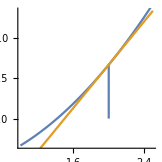
Otra posibilidad es considerar, en lugar de la recta que pasa por dos puntos de la gráfica, la recta tangente a ésta en un punto. 

Dada una aproximación inicial x_0, la recta tangente en (x_0, f(x_0)) sería y=f(x_0) + f ‘(x_0) (x-x_0), que se anula en el punto 

			x_1 = x_0 - (f(x_0))/(f'(x_0))

En general, podemos construir la sucesión 

			x_(n+1) = x_n - (f(x_n))/(f'(x_n))
Se trata del método de Newton. Se elige una aproximación inicial, se calcula la recta tangente a la gráfica de la función y se considera el punto donde la recta corta al eje horizontal. Es decir, sustituimos la función por un polinomio y consideramos como nueva aproximación a la raíz de la función, la raíz del polinomio.

En nuestro ejemplo, para la función x^2-2, y si tomamos x0=2 como punto inicial, la recta tangente es f(x0)+f ’(x0)(x-x0) = 2 + 4(x-2), que se anula en 2+4(x-2)=0, x= 3/2=1.5  

			-Graphics-
Convergencia del Método de Newton.
Si nos encontramos con una función f
	1) continua en un intervalo [a,b], 
	2) con cambio de signo en el intervalo (f(a)*f(b)<0), 
	3) con derivada no nula en el intervalo 
	4) con derivada segunda siempre positiva o siempre negativa, 
el método de Newton generará una sucesión convergente a una solución de f(x)=0 si partimos del extremo donde la función tiene el mismo signo que la derivada segunda. La sucesión que se crea es monótona. En estas circunstancias, la convergencia del método de Newton es cuadrática. Es decir, cuando estamos “cerca” de la solución el error (diferencia entre la raíz y la aproximación) se eleva al cuadrado en cada paso. Más concretamente,
		 Lim_(n → ∞) (|x_(n+1)-s|)/(|x_n-s|^2) = α >0.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=x^2-2
```

```mathematica
s=4;Do[s=s-f[s]/f'[s],{10}];Print["Una aproximación sería ",N[s,10],". La función vale ",N[f[s],10]]
```

Una aproximación sería 1.414213562. La función vale 1.810236572×10^-328

Si queremos ver todos los pasos intermedios y los valores de f.

```mathematica
s=4; i=0;Print["Con la aproximación inicial, i=0, ",N[s,15],". La función vale ",N[f[s],15]];
Do[i=i+1;s=s-f[s]/f'[s];Print["La siguiente aproximación sería, para i=",i,", valor ", N[s,20],", donde la función vale ",N[f[s],15]],{10}]
```

Con la aproximación inicial, i=0, 4.. La función vale 14.

La siguiente aproximación sería, para i=1, valor 2.25, donde la función vale 3.0625

La siguiente aproximación sería, para i=2, valor 1.5694444444444444444, donde la función vale 0.463155864197531

La siguiente aproximación sería, para i=3, valor 1.4218903638151425762, donde la función vale 0.0217722067103585

La siguiente aproximación sería, para i=4, valor 1.4142342859400733411, donde la función vale 0.0000586155284291247

La siguiente aproximación sería, para i=5, valor 1.414213562524932065, donde la función vale 4.29459935117672×10^-10

La siguiente aproximación sería, para i=6, valor 1.4142135623730950488, donde la función vale 2.30544794789589×10^-20

La siguiente aproximación sería, para i=7, valor 1.4142135623730950488, donde la función vale 6.64386280057171×10^-41

La siguiente aproximación sería, para i=8, valor 1.4142135623730950488, donde la función vale 5.51761411410257×10^-82

La siguiente aproximación sería, para i=9, valor 1.4142135623730950488, donde la función vale 3.80550818901799×10^-164

La siguiente aproximación sería, para i=10, valor 1.4142135623730950488, donde la función vale 1.81023657208537×10^-328

Si queremos ver el error en cada paso.

```mathematica
s=4; i=0;Print["Con la aproximación inicial, i=0, ",N[s,15],". La función vale ",N[f[s],15]];
Do[i=i+1;s=s-f[s]/f'[s];Print["La siguiente aproximación sería, para i=",i,", valor ", N[s,20],", donde el error es ",N[s-Sqrt[2],15]],{7}]
```

Con la aproximación inicial, i=0, 4.. La función vale 14.

La siguiente aproximación sería, para i=1, valor 2.25, donde el error es 0.835786437626905

La siguiente aproximación sería, para i=2, valor 1.5694444444444444444, donde el error es 0.155230882071349

La siguiente aproximación sería, para i=3, valor 1.4218903638151425762, donde el error es 0.00767680144204753

La siguiente aproximación sería, para i=4, valor 1.4142342859400733411, donde el error es 0.0000207235669782923

La siguiente aproximación sería, para i=5, valor 1.414213562524932065, donde el error es 1.51837016176669×10^-10

La siguiente aproximación sería, para i=6, valor 1.4142135623730950488, donde el error es 8.15098938814897×10^-21

La siguiente aproximación sería, para i=7, valor 1.4142135623730950488, donde el error es 2.34896021977865×10^-41

Observamos la rapidez con la que el método de Newton se acerca a la solución. Partiendo del 4, las sucesivas aproximaciones se han ido acercando a la raíz cuadrada de dos con mucha rapidez. En la quinta iteración ya teníamos un error de 10 elevado a -10, a la siguiente elevado a -21 y a la siguiente a -41. Como decíamos al hablar de la convergencia cuadrática de Newton el error, cuando estamos cerca de la solución, en cada paso se eleva al cuadrado.

# Funcionamiento del método de Newton.

El método de Newton es un método muy interesante, aunque dependiendo del punto inicial podría converger o no, o hacerlo a una u otra raíz.

Por ejemplo, para la ecuación Log(x)=0, el método de Newton converge si el punto inicial está en el intervalo (0,e). En otro caso, la tangente manda a valores negativos y no funcionaría el método.

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:=Log[x]
```

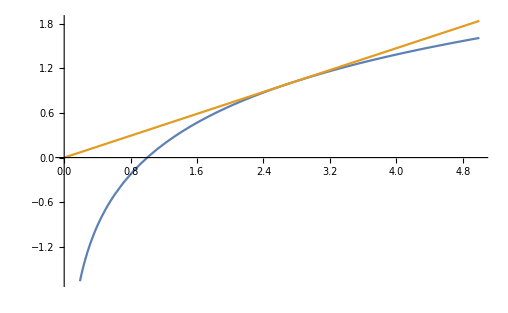

```mathematica
Plot[{f[x],1+(x-E)/E},{x,0,5}]
```

```mathematica
x=E-0.001;
Do[x=x-f[x]/f'[x];Print[x],{10}];Print["Una aproximación sería ",x,". La función vale ",f[x]]
```

0.000999816

0.00790648

0.0461744

0.188176

0.502501

0.848301

0.987863

0.999926

1.

1.

Una aproximación sería 1.. La función vale 0.

Por ejemplo, para la ecuación x^2-2=0, el método de Newton converge a √2 si empezamos con un punto del intervalo (0,∞) y a -√2 si empezamos con un punto del intervalo (-∞,0). Finalmente, si empezamos en el punto x=0, el método no converge pues la tangente no corta el eje horizontal.

```mathematica
Clear[f]
```

```mathematica
f[x_]:= x^2-2
```

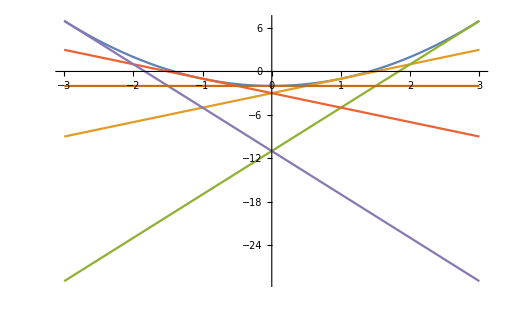

```mathematica
Plot[{f[x],f[1]+f'[1](x-1), f[3]+f'[3](x-3), f[-1]+f'[-1](x+1),f[-3]+f'[-3](x+3),f[0]},{x,-3,3}]
```

```mathematica
x=3.;
Do[x=x-f[x]/f'[x];Print[x],{10}];Print["Una aproximación sería ",x,". La función vale ",f[x]]
```

1.83333

1.46212

1.415

1.41421

1.41421

1.41421

«4 more identical outputs»

Una aproximación sería 1.41421. La función vale -4.44089×10^-16

```mathematica
x=-1.;
Do[x=x-f[x]/f'[x];Print[x],{10}];Print["Una aproximación sería ",x,". La función vale ",f[x]]
```

-1.5

-1.41667

-1.41422

-1.41421

-1.41421

-1.41421

«4 more identical outputs»

Una aproximación sería -1.41421. La función vale -4.44089×10^-16

#### Cálculo de todas las raíces

En general, cuando estamos cerca de una solución, el método de Newton nos llevará hasta la solución.

Cuando nos encontramos con una ecuación podríamos comenzar con un punto inicial cualquiera. Si tenemos convergencia hacia una solución, podríamos preguntarnos si habrá más soluciones. Una idea es comenzar con otros puntos iniciales y ver qué ocurre. Podría ocurrir que así encontrásemos varias, o que siempre nos mandase a la misma o que no funcionase el método de Newton. Nos quedaría la duda de si hay más raíces y cómo conseguir hallarlas todas. 

Además de probar con diferentes puntos iniciales, otra posibilidad es intentar “quitarle” la raíz a la ecuación e intentar buscar otras. Se trata del método de deflación. Si partimos de la ecuación f(x)=0 y hemos encontrado una raíz aproximada r, podríamos considerar la función g(x)=f(x)/(x-r) e intentar hallar nuevas aproximaciones de la solución de g(x)=0 (aunque esa aproximación la refinemos en la ecuación f(x)=0, pues realmente r no es una solución exacta).

Por ejemplo, sea la ecuación x^7-2x^5+4 x^2-2x-6 = 0.

Probamos con varios puntos iniciales.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:= x^7-2 x^5+4 x^2-2x-6
```

```mathematica
s=3.;
Do[s=s-f[s]/f'[s],{20}];Print["Una aproximación sería ",s,". La función vale ",f[s]]
```

Una aproximación sería 1.44444. La función vale -5.32907×10^-15

Una solución aproximada sería 1.44444. Probamos con otro punto inicial.

```mathematica
s=-3.;
Do[s=s-f[s]/f'[s],{20}];Print["Una aproximación sería ",s,". La función vale ",f[s]]
```

Una aproximación sería -1.63704. La función vale -5.32907×10^-15

Una solución aproximada sería -1.63704. Probamos con otro punto inicial.

```mathematica
s=5.;
Do[s=s-f[s]/f'[s],{20}];Print["Una aproximación sería ",s,". La función vale ",f[s]]
```

Una aproximación sería 1.44444. La función vale -5.32907×10^-15

Volvemos a encontrar la misma raíz. Probamos con otro punto inicial.

```mathematica
s=-10.;
Do[s=s-f[s]/f'[s],{20}];Print["Una aproximación sería ",s,". La función vale ",f[s]]
```

Una aproximación sería -1.63704. La función vale 6.66134×10^-15

Volvemos a encontrar la misma raíz. Tras probar con varios puntos iniciales y no encontrar raíces, podemos “quitar” las raíces encontradas a la ecuación inicial.

```mathematica
g[x_]:=f[x]/((x-1.44444)(x+1.63704))
```

Ahora tratamos de encontrar raíces de esta nueva ecuación.

```mathematica
s=1.;
Do[s=s-g[s]/g'[s],{20}];Print["Una aproximación sería ",s,". La función vale ",g[s]]
```

Una aproximación sería -0.921146. La función vale 5.24461×10^-16

Hemos encontrado una nueva raíz, -0.921146, Podemos probar con otro punto inicial, o “quitar” esta nueva raíz.

```mathematica
h[x_]:=g[x]/(x+0.921146)
```

Ahora tratamos de encontrar raíces de esta nueva ecuación.

```mathematica
s=1.;
Do[s=s-h[s]/h'[s],{20}];Print["Una aproximación sería ",s,". La función vale ",h[s]]
```

Una aproximación sería -1.93161. La función vale 33.5982

El valor que ha aparecido tras hacer 20 iteraciones del método de Newton no es una raíz (no es una aproximación de una raíz) pues el valor de la función es 33.5982. Probamos con otro punto inicial.

```mathematica
s=7.;
Do[s=s-h[s]/h'[s],{20}];Print["Una aproximación sería ",s,". La función vale ",h[s]]
```

Una aproximación sería 0.884872. La función vale 2.07876

El valor que ha aparecido tras hacer 20 iteraciones del método de Newton tampoco es una raíz (no es una aproximación de una raíz) pues el valor de la función es no es muy cercano a cero. Podría ser que la función no tenga más ceros.

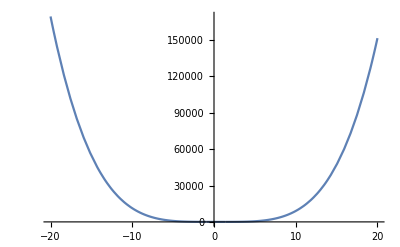
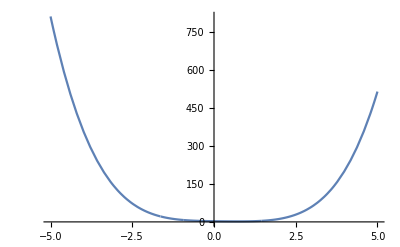
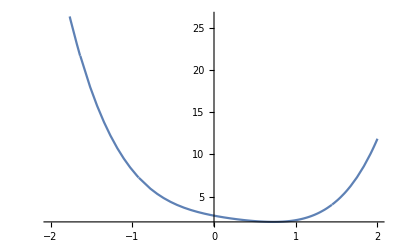
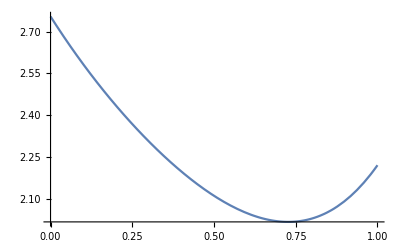

```mathematica
{Plot[h[x],{x,-20,20}],Plot[h[x],{x,-5,5}],Plot[h[x],{x,-2,2}],Plot[h[x],{x,0,1}]}
```

A la vista de las gráficas, parece que no tiene raíces. El Mathematica también tiene una función para buscar soluciones aproximadas.

```mathematica
Solve[f[x]==0,x]
```

{{x→Root[-6-2 #1+4 #1^2-2 #1^5+#1^7&,1]},{x→Root[-6-2 #1+4 #1^2-2 #1^5+#1^7&,2]},{x→Root[-6-2 #1+4 #1^2-2 #1^5+#1^7&,3]},{x→Root[-6-2 #1+4 #1^2-2 #1^5+#1^7&,4]},{x→Root[-6-2 #1+4 #1^2-2 #1^5+#1^7&,5]},{x→Root[-6-2 #1+4 #1^2-2 #1^5+#1^7&,6]},{x→Root[-6-2 #1+4 #1^2-2 #1^5+#1^7&,7]}}

```mathematica
NSolve[f[x]==0,x]
```

{{x→-1.63704},{x→-0.921146},{x→-0.463502-1.20194 ⅈ},{x→-0.463502+1.20194 ⅈ},{x→1.02038-0.78661 ⅈ},{x→1.02038+0.78661 ⅈ},{x→1.44444}}

El Mathematica ha obtenido tres raíces reales y dos parejas de raíces complejas conjugadas. Parece que no había más soluciones.

También podemos considerar funciones que no sean polinómicas.

```mathematica
Clear[f]
```

```mathematica
f[x_]:=3x+2-ⅇ^x
```

```mathematica
Plot[f[x],{x,-1,3}]
```

-Graphics-

```mathematica
x=4.;
Do[x=x-f[x]/f'[x],{10}];Print["Una aproximación sería ",x,". La función vale ",f[x]]
```

Una aproximación sería 2.12539. La función vale 0.

```mathematica
Clear[x]
```

```mathematica
g[x_]:=f[x]/(x-2.12539119881113)
```

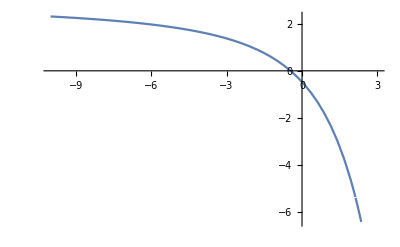

```mathematica
Plot[g[x],{x,-10,3}]
```

```mathematica
x=4.;
Do[x=x-g[x]/g'[x],{10}];Print["Una aproximación sería ",x,". La función vale ",g[x]]
```

Una aproximación sería -0.455233. La función vale -8.6043×10^-17

```mathematica
x=-0.4552333555851903;
Do[x=x-f[x]/f'[x],{10}];Print["Una aproximación sería ",x,". La función vale ",f[x]]
```

Una aproximación sería -0.455233. La función vale 2.22045×10^-16

```mathematica
Clear[x]
```

```mathematica
h[x_]:=f[x]/((x-2.12539119881113)*(x+0.4552333555851904))
```

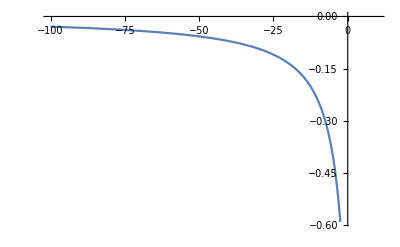

```mathematica
Plot[h[x],{x,-100,10}]
```

```mathematica
x=4.;
Do[x=x-h[x]/h'[x],{10}];Print["Una aproximación sería ",x,". La función vale ",g[x]]
```

Una aproximación sería -906.158. La función vale 2.99078

La función parece no tener más raíces. Podemos probar con otros puntos iniciales o dibujar la gráfica. Y también podemos hacer el estudio completo de la función para ver si tiene más raíces.